```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data = RandomVariate[NormalDistribution[4.5,2],{5}]
```

{1.37455,0.15621,5.67303,4.64689,3.2766}

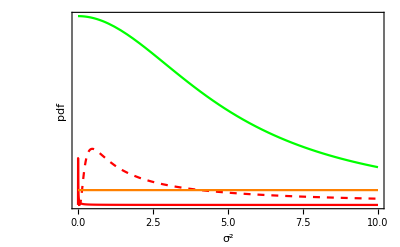

```mathematica
aUpper = 100;
gPrior1= Plot[{PDF[TruncatedDistribution[{0,∞},CauchyDistribution[0,5]],x],PDF[InverseGammaDistribution[0.0001,0.0001],x],PDF[InverseChiSquareDistribution[0.1],x],PDF[UniformDistribution[{0,aUpper}],x]},{x,0,10},PlotRange->Full,PlotStyle->{Green,Red,{Red,Dashed},Orange},Epilog->{Dashed,Red,Line[{{aUpper,0},{aUpper,PDF[UniformDistribution[{0,aUpper}],aUpper]}}]},Frame->{True,True,False,False},FrameTicks->{True,False},BaseStyle->Medium,FrameLabel->{Superscript[σ,2],"pdf"}]
```

## Importing data from Stan fits

```mathematica
fit1 = Flatten@Import["distributions_halfcauchy1.csv"][[2;;]];
fit2 = Flatten@Import["distributions_halfcauchy2.csv"][[2;;]];
fit3 = Flatten@Import["distributions_halfcauchy3.csv"][[2;;]];
fit4 = Flatten@Import["distributions_halfcauchy4.csv"][[2;;]];
```

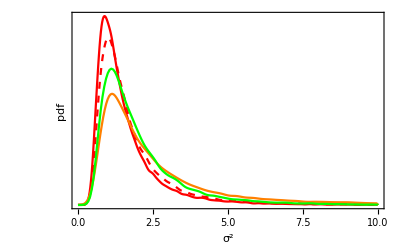

```mathematica
gPosterior=SmoothHistogram[{fit2,fit3,fit4,fit1},PlotRange->{{0,10},Full},PlotStyle->{Red,{Red,Dashed},Orange,Green},Frame->{True,True,False,False},FrameTicks->{True,False},BaseStyle->Medium,FrameLabel->{Superscript[σ,2],"pdf"}]
```

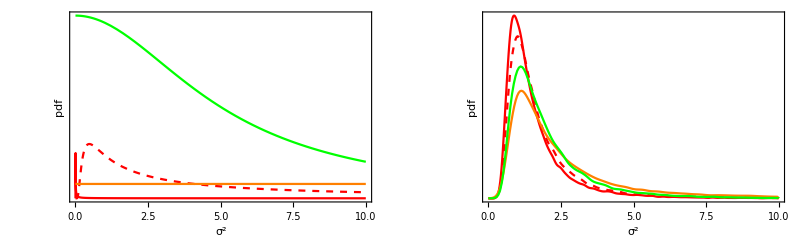

```mathematica
gFinal=Show[GraphicsRow[{gPrior1,gPosterior}],ImageSize->800]
```

```mathematica
Export["Distributions_halfCauchyPrior.pdf",gFinal]
```

Distributions_halfCauchyPrior.pdf